```mathematica
SetOptions[EvaluationNotebook[],LightDark->"Light"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
constructLatticeLikeChain[θ_,α_,circumference_]:= 

(* no attempt to make this periodic, just use as a starter condition *)
Module[{upVector,downVector,addVector,chain,stopChain},
upVector= { Cos[α],Sin[α]};
downVector = { -Cos[α+θ],Sin[α+θ]};
addVector[ch_] := Module[{},
If[ N[ Last[ch]+downVector][[2]] <0,Append[ch,Last[ch]+upVector],Append[ch,Last[ch]+downVector]]
];

continueTest[ch_] := Module[{x},
x=N[ (Last[ch]+downVector)[[1]]];
x<circumference
];
chain=NestWhile[addVector,{{0,0}},
continueTest,1,1000
];
chain
];
constructLatticeLikeChain[2π/5,π/7,1]//N
```

{{0.,0.},{0.134233,0.99095},{0.268467,1.9819},{0.4027,2.97285},{0.536933,3.9638},{0.671166,4.95475},{0.8054,5.9457},{0.939633,6.93665}}

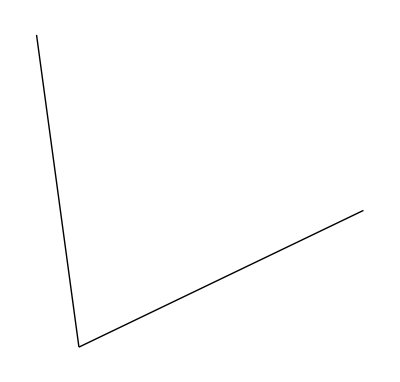

```mathematica
gtheta= 2π/5;
gAlpha = π/7;
Graphics[{Line[{{0,0},{Cos[gAlpha],Sin[gAlpha]}}],Line[{{0,0},{Cos[gAlpha+gtheta],Sin[gAlpha+gtheta]}}]}]
```

## Random analysis

An n-chain with width C is a series of touching disks of radius 1 whose centres have increasing y-coordinate and for which the n+1 disk is a translation of the first by (C,0).
A reversing n-chain drops the requirement that the centres are increasing. An n-chain or a reversing n-chain is feasible if it can be constructed from n iterations of a stacked-disk model.

The vector joining the ith centre to the i+1-thcentre is v_i and makes an angle α_i with the positive x-axis.

For an n-chain,
C= Σ |Cos α_i|

Suppose the chain forms part of an opposed lattice on a cylinder C with parastichy vectors p_m and p_n and  p_m is the one with positive x component. Then there are  n  of the  p_m vectors and m  of the p_n  ones because eg

n p_m - m p_n= (C,0)

so

n Cos α_m +m| Cos α_n|= C
nSin α_m - m sin α_n=0

Suppose we rotate each p_m by a further ψ towards the axis so that Cos α_m is increased to  Cos α_m

```mathematica
TrigExpand[(n Cos Subscript[α, m] +m Abs[ Cos Subscript[α, n]]) ] /. Subscript[α, m]->Subscript[α, m]-Subscript[ψ, m]
```

Cos[α] Cos[ψ]+Sin[α] Sin[ψ]

```mathematica
( n Cos [Subscript[α, m] ]+m Abs[Cos[ Subscript[α, n]] )
```

```mathematica
TrigExpand[(n Cos[Subscript[α, m]]+ m Abs[ Cos[Subscript[α, n]]])/. {Subscript[α, m]->Subscript[α, m]-Subscript[ψ, m] ,Subscript[α, n]->Subscript[α, n]+Subscript[ψ, n] }]
```

ReplaceRepeated::rrlim: Exiting after m Abs[Cos[α_n]]+n Cos[α_m] scanned 65536 times.

```mathematica
Cos [Subscript[α, m] ]+m Abs[ Cos[ Subscript[α, n]]
```

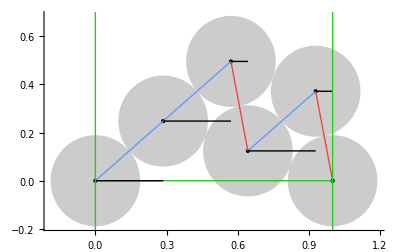

```mathematica
Graphics[pmPlot[{2,3},π/3],Axes->True]
```

```mathematica
testChain=<|1->Disk[{0,0},1/(2 √7)],2->Disk[{1,0},1/(2 √7)],3->Disk[{9/14,(√3)/14},1/(2 √7)],4->Disk[{2/7,(√3)/7},1/(2 √7)],5->Disk[{13/14,(3 √3)/14},1/(2 √7)],6->Disk[{4/7,(2 √3)/7},1/(2 √7)],
7->Disk[{1,0},1/(2 √7)]|>
```

```mathematica
diskCentre/@Values[testChain]
```

```mathematica
centres={{9/14,(√3)/14},{2/7,(√3)/7},{13/14,(3 √3)/14},{4/7,(2 √3)/7}}
```

{{9/14,(√3)/14},{2/7,(√3)/7},{13/14,(3 √3)/14},{4/7,(2 √3)/7}}

## Lattice formulae

The general formula for touching - circle lattices

```mathematica
tf=<|"z1"->(v-u Cos[θ]-ⅈ u Sin[θ])/(n-m Cos[θ]-ⅈ m Sin[θ]),"zm"->Δ (-u+(m (v-u Cos[θ]-ⅈ u Sin[θ]))/(n-m Cos[θ]-ⅈ m Sin[θ])),"zn"->Δ (-v+(n (v-u Cos[θ]-ⅈ u Sin[θ]))/(n-m Cos[θ]-ⅈ m Sin[θ])),"pm"->{(n-m Cos[θ])/(m^2+n^2-2 m n Cos[θ]),(m Sin[θ])/(m^2+n^2-2 m n Cos[θ])},

"pmRadius"->4 radius^2*{n-m Cos[θ],m Sin[θ]},
"pn"->{(-m+n Cos[θ])/(m^2+n^2-2 m n Cos[θ]),(n Sin[θ])/(m^2+n^2-2 m n Cos[θ])},
"pnRadius"->4 radius^2*{-m+n Cos[θ],n Sin[θ]},
"radius"-> 1/2 √(1/(m^2+n^2-2 m n Cos[θ])),
"tanAlpham"->(m Sin[θ])/(n-m Cos[θ]),"tanAlphan"->(n Sin[θ])/(-m+n Cos[θ]),"h"->(Δ Sin[θ])/(m^2+n^2-2 m n Cos[θ]),"d"->(m u+n v-(n u+m v) Cos[θ])/(m^2+n^2-2 m n Cos[θ]),"Γ"->m^2+n^2-2 m n Cos[θ],"hGamma"->(Δ Sin[θ])/Γ,"dGamma"->(m u+n v-(n u+m v) Cos[θ])/Γ,"dAxisRange"->{}|>;
```

```mathematica
pm[θ_,{m_,n_}] := Evaluate[tf["pm"]];
pn[θ_,{m_,n_}] := Evaluate[tf["pn"]];
Clear[r2];
r2[θ_,{m_,n_}] := Evaluate[tf["pm"].tf["pm"]/4];
diskRadius[θ_,{m_,n_}] := Sqrt[r2[θ,{m,n}]];

makeChain[{m_,n_},θ_,sf_] := Module[{pmvec,pnvec,chain},
pmvec=  sf*pm[θ,{m,n}];
pnvec= sf*pn[θ,{m,n}];

dr=Sqrt[pmvec.pmvec]/2;
chain=Nest[nextPoint[#,pmvec,pnvec]&,{{0,0}},m+n];
chain=SortBy[chain,Last];
chain=Association@MapIndexed[First[#2]->Disk[#1,dr]&,chain]
];

diskCentre[Disk[xy_,___]]:=xy;
chainPoints[chain_] := Map[diskCentre,chain];
chainVectors[chain_] := Module[{res,chainOrder},
chainOrder=SortBy[chain,First];
res=Partition[Values[chainPoints[chainOrder]],2,1];
res
];
colouredVectors[chain_] := Module[{res},
res=chainVectors[chain];
Map[{If[#[[1,2]]>#[[2,2]],StandardRed,StandardBlue],Line[#]}&,res]
];

chainXSteps[chain_] :=  Module[{res},
res=chainVectors[chain];
res=Map[ {#[[1]],{#[[2]][[1]],#[[1]][[2]]}}&,res];
res
];

ffs=Directive[FaceForm[Opacity[0.2],LightGray]];
pmPlot[{m_,n_},θ_] := Module[{pmvecz,pnvecz},
r2Scale=N@diskRadius[θ,{m,n}];
sf=1;
chain=makeChain[{m,n},
θ,sf];
{
ffs,Values[chain],
Point[Values[chainPoints[chain]]],
colouredVectors[chain],
{StandardGreen,InfiniteLine[{{0,0},{0,1}}],
InfiniteLine[sf*{{1,0},{1,1}}],Line[{{0,0},{sf,0}}]}
,Map[Line,chainXSteps[chain]]

}
];
```

```mathematica
chainXSteps[chain]
```

{{{0,0},{0.324814,0}},{{0.324814,0.170765},{0.649627,0.170765}},{{0.649627,0.341529},{0.912407,0.341529}},{{0.912407,0.0853823},{1.23722,0.0853823}},{{1.23722,0.256147},{1.5,0.256147}}}

{{0,0},{(4-3/4 (1-√5))/(25-6 (1-√5)),(3 √(5/8+(√5)/8))/(25-6 (1-√5))},{(2 (4-3/4 (1-√5)))/(25-6 (1-√5)),(6 √(5/8+(√5)/8))/(25-6 (1-√5))},{-(-2-√5)/(25-6 (1-√5))+(2 (4-3/4 (1-√5)))/(25-6 (1-√5)),(2 √(5/8+(√5)/8))/(25-6 (1-√5))}}

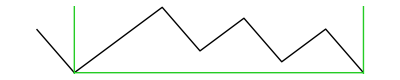

```mathematica
nextPoint[pointList_,pmvec_,pnvec_] := Module[{up,down},
down= Last[pointList ]- pnvec;
If[Chop[down[[2]]]>=0,
Return[Append[pointList,down]]];
up= Last[pointList]+ pmvec;
Return[Append[pointList,up]];
];
```

```mathematica
addByAngle[centres_,angle_] :=Append[centres,Last[centres]+2*(N@{Cos[angle],Sin[angle]})];
```

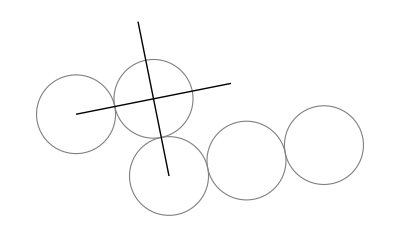

```mathematica
angle=N@Abs[angleForOrthogonalLatticeChain[{2,3},4]];
pm=2*{Cos[angle],Sin[angle]};
pn = 2*{Cos[angle+π/2],Sin[angle+π/2]};
angles={angle,angle-π/2,angle,angle};
centres=Fold[addByAngle,{{-4,0}},angles];
ffs=Directive[FaceForm[None],EdgeForm[Gray]];
Graphics[{ffs,Disk[#,1]&/@centres,
Line[{{centres[[1]], centres[[1]]+2 pm},{centres[[2]]-pn, centres[[2]]+ pn}}]}]
```

```mathematica
centres
```

{{-4,0},{-2.03884,0.392232},{-1.64661,-1.56893},{-2.03884,0.392232}}